```mathematica
SetDirectory[NotebookDirectory[]];
```

## Read matrix

```mathematica
ReadMatrixSparse[directoryname_,filename_]:=Module[{nnz,result,sparseformat},

sparseformat = Import[StringJoin[directoryname,"/",filename],"Table"];

(*converting to mathematica format*)
sparseformat⟦All,1⟧=sparseformat⟦All,1⟧+1;
sparseformat⟦All,2⟧=sparseformat⟦All,2⟧+1;
sparseformat = Table[sparseformat⟦ii,{1,2}⟧->sparseformat⟦ii,3⟧,{ii,1,Length[sparseformat]}];
result = SparseArray[sparseformat]

]

ReadMatrixFull[directoryname_,filename_]:=Module[{result},

result = Import[StringJoin[directoryname,"/",filename],"Table"];
result
]
```

```mathematica
ReadVector[filename_]:=Module[{nnz,result,sparseformat},
Flatten[Import[filename,"Table"]]
]
```

## Comparisions

### Poisson Heat Conduction

```mathematica
directoryname="/Users/neerajsarna/sciebo/DG_moments_deal/Tests/build/printed_matrices";
filename = "cell_matrix_internal0";
MatG20 = ReadMatrixFull[directoryname,filename];

filename = "cell_matrix_internal1";
MatG26 = ReadMatrixFull[directoryname,filename];

filename = "cell_matrix_internal2";
MatG35 = ReadMatrixFull[directoryname,filename];

filename = "cell_matrix_internal3";
MatG45 = ReadMatrixFull[directoryname,filename];

(*matrices from code which is not m adapted*)
filename = "cell_matrix_original_-0.375_6";
MatG20Original = ReadMatrixFull[directoryname,filename];

filename = "cell_matrix_original_-0.125_8";
MatG26Original = ReadMatrixFull[directoryname,filename];

filename = "cell_matrix_original_0.125_9";
MatG35Original = ReadMatrixFull[directoryname,filename];

filename = "cell_matrix_original_0.375_11";
MatG45Original = ReadMatrixFull[directoryname,filename];
```

```mathematica
MatrixPlot[(MatG45-MatG45Original)]
```

-Graphics-

### Manuel and Meshworker assembly comparision

```mathematica
directoryname="/Users/neerajsarna/sciebo/DG_moments_deal/Tests/build/printed_matrices";
filename = "global_matrix_meshworker";
MatMeshworker = ReadMatrixSparse[directoryname,filename];

filename = "global_matrix_manuel";
MatManuel = ReadMatrixSparse[directoryname,filename];
```

```mathematica
Norm[MatMeshworker-MatManuel]
```

0.

```mathematica
?MatrixPlot
```

MatrixPlot[m] generates a plot that gives a visual representation of the values of elements in a matrix.

### Heat Conduction Global matrix

```mathematica
directoryname="/Users/neerajsarna/sciebo/DG_moments_deal/Tests/build/printed_matrices";
filename = "global_matrix_heat_conduction";
MatHeatConduction = ReadMatrixSparse[directoryname,filename];
```

```mathematica
temMat = ConstantArray[0,{52,52}];
```

```mathematica
CForm[Flatten[Chop[Normal[MatHeatConduction]]]]
```

List(0.265965,2.e-6,0.132981,0,0.166667,0.166667,0.083333,0.083333,0.166667,0.083333,
   0.166667,0.083333,-0.108581,-1.e-6,-0.054289,0,0.14832,0,0.07416,0,0,0,0,0,-0.039739,
   2.e-6,-0.019871,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2.e-6,7.e-6,0,
   2.e-6,-0.166667,-0.166667,-0.083333,-0.083333,0.083333,0.166667,0.083333,0.166667,
   -1.e-6,-5.e-6,0,-1.e-6,0,3.e-6,0,2.e-6,0,0,0,0,2.e-6,3.e-6,0,0,0,0,0,0,0,0,0,0,0,0,0,
   0,0,0,0,0,0,0,0,0,0,0,0,0,0.132981,0,0.531923,0.132981,0.083333,0.083333,0.166667,
   0.166667,-0.166667,-0.083333,-0.166667,-0.083333,-0.054289,0,-0.217157,-0.054289,
   0.07416,0,0.108578,-0.019871,0,0,0,0,-0.019871,0,0.108578,0.07416,0,0,0,0,0,0,0,0,0,
   0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2.e-6,0.132981,0.265965,-0.083333,-0.083333,
   -0.166667,-0.166667,-0.083333,-0.166667,-0.083333,-0.166667,0,-1.e-6,-0.054289,
   -0.108581,0,2.e-6,-0.019871,-0.039739,0,0,0,0,0,0,0.07416,0.14832,0,0,0,0,0,0,0,0,0,
   0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.166667,0.166667,-0.083333,0.083333,0.265962,
   0.132981,0,0,0,0,0,0,0.136083,-0.136083,0.068041,-0.068041,-0.185893,0.185893,
   -0.092946,0.092946,0.166667,0.083333,0.166667,0.083333,0.04981,-0.04981,0.024905,
   -0.024905,-0.168209,-0.084104,0,0,0,0,0,0,-0.11979,-0.059895,0,0,0,0,0,0,0.314368,
   0.157184,0,0,0,0,0,0,-0.166667,0.166667,-0.083333,0.083333,0.132981,0.265962,0,0,0,0,
   0,0,0.136083,-0.136083,0.068041,-0.068041,-0.185893,0.185893,-0.092946,0.092946,
   0.083333,0.166667,0.083333,0.166667,0.04981,-0.04981,0.024905,-0.024905,-0.084104,
   -0.168209,0,0,0,0,0,0,-0.059895,-0.11979,0,0,0,0,0,0,0.157184,0.314368,0,0,0,0,0,0,
   -0.083333,0.083333,-0.166667,0.166667,0,0,0.265962,0.132981,0,0,0,0,0.068041,
   -0.068041,0.136083,-0.136083,-0.092946,0.092946,-0.185893,0.185893,-0.166667,
   -0.083333,-0.166667,-0.083333,0.024905,-0.024905,0.04981,-0.04981,0,0,-0.168209,
   -0.084104,0,0,0,0,0,0,-0.11979,-0.059895,0,0,0,0,0,0,0.314368,0.157184,0,0,0,0,
   -0.083333,0.083333,-0.166667,0.166667,0,0,0.132981,0.265962,0,0,0,0,0.068041,
   -0.068041,0.136083,-0.136083,-0.092946,0.092946,-0.185893,0.185893,-0.083333,
   -0.166667,-0.083333,-0.166667,0.024905,-0.024905,0.04981,-0.04981,0,0,-0.084104,
   -0.168209,0,0,0,0,0,0,-0.059895,-0.11979,0,0,0,0,0,0,0.157184,0.314368,0,0,0,0,
   -0.166667,-0.083333,0.166667,0.083333,0,0,0,0,0.265962,0,0.132981,0,0.136083,
   0.068041,-0.136083,-0.068041,0.04981,0.024905,-0.04981,-0.024905,0.166667,0.166667,
   0.083333,0.083333,-0.185893,-0.092946,0.185893,0.092946,0,0,0,0,-0.168209,0,
   -0.084104,0,0,0,0,0,0.314368,0,0.157184,0,0,0,0,0,-0.11979,0,-0.059895,0,-0.083333,
   -0.166667,0.083333,0.166667,0,0,0,0,0,0.265962,0,0.132981,0.068041,0.136083,
   -0.068041,-0.136083,0.024905,0.04981,-0.024905,-0.04981,-0.166667,-0.166667,
   -0.083333,-0.083333,-0.092946,-0.185893,0.092946,0.185893,0,0,0,0,0,-0.168209,0,
   -0.084104,0,0,0,0,0,0.314368,0,0.157184,0,0,0,0,0,-0.11979,0,-0.059895,-0.166667,
   -0.083333,0.166667,0.083333,0,0,0,0,0.132981,0,0.265962,0,0.136083,0.068041,
   -0.136083,-0.068041,0.04981,0.024905,-0.04981,-0.024905,0.083333,0.083333,0.166667,
   0.166667,-0.185893,-0.092946,0.185893,0.092946,0,0,0,0,-0.084104,0,-0.168209,0,0,0,0,
   0,0.157184,0,0.314368,0,0,0,0,0,-0.059895,0,-0.11979,0,-0.083333,-0.166667,0.083333,
   0.166667,0,0,0,0,0,0.132981,0,0.265962,0.068041,0.136083,-0.068041,-0.136083,
   0.024905,0.04981,-0.024905,-0.04981,-0.083333,-0.083333,-0.166667,-0.166667,
   -0.092946,-0.185893,0.092946,0.185893,0,0,0,0,0,-0.084104,0,-0.168209,0,0,0,0,0,
   0.157184,0,0.314368,0,0,0,0,0,-0.059895,0,-0.11979,-0.108581,-1.e-6,-0.054289,0,
   -0.136083,-0.136083,-0.068041,-0.068041,-0.136083,-0.068041,-0.136083,-0.068041,
   0.75356,0.177309,0.199471,0,-0.149205,0.016225,-0.090828,0,0,0,0,0,-0.072432,
   -0.060553,0.024337,0,0.215166,0.215166,0.107583,0.107583,0.215166,0.107583,0.215166,
   0.107583,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1.e-6,-5.e-6,0,-1.e-6,0.136083,0.136083,
   0.068041,0.068041,-0.068041,-0.136083,-0.068041,-0.136083,0.177309,0.709235,0,
   0.177309,0.016225,-0.088656,0,-0.060553,0,0,0,0,-0.060553,-0.088656,0,0.016225,
   -0.215166,-0.215166,-0.107583,-0.107583,0.107583,0.215166,0.107583,0.215166,0,0,0,0,
   0,0,0,0,0,0,0,0,0,0,0,0,-0.054289,0,-0.217157,-0.054289,-0.068041,-0.068041,
   -0.136083,-0.136083,0.136083,0.068041,0.136083,0.068041,0.199471,0,0.797885,0.199471,
   -0.090828,0,-0.132981,0.024337,0,0,0,0,0.024337,0,-0.132981,-0.090828,0.107583,
   0.107583,0.215166,0.215166,-0.215166,-0.107583,-0.215166,-0.107583,0,0,0,0,0,0,0,0,0,
   0,0,0,0,0,0,0,0,-1.e-6,-0.054289,-0.108581,0.068041,0.068041,0.136083,0.136083,
   0.068041,0.136083,0.068041,0.136083,0,0.177309,0.199471,0.75356,0,-0.060553,0.024337,
   -0.072432,0,0,0,0,0,0.016225,-0.090828,-0.149205,-0.107583,-0.107583,-0.215166,
   -0.215166,-0.107583,-0.215166,-0.107583,-0.215166,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,
   0.14832,0,0.07416,0,0.185893,0.185893,0.092946,0.092946,-0.04981,-0.024905,-0.04981,
   -0.024905,-0.149205,0.016225,-0.090828,0,1.903057,0.694475,0.812609,0.277778,0,0,0,0,
   -0.110818,-0.022164,-0.033245,0,-0.117569,-0.117569,-0.058784,-0.058784,0.031502,
   0.015751,0.031502,0.015751,0.219199,0.219199,0.1096,0.1096,0.170859,0.08543,0.170859,
   0.08543,-0.021522,-0.021522,-0.010761,-0.010761,-0.008569,-0.004285,-0.008569,
   -0.004285,0,3.e-6,0,2.e-6,-0.185893,-0.185893,-0.092946,-0.092946,-0.024905,-0.04981,
   -0.024905,-0.04981,0.016225,-0.088656,0,-0.060553,0.694475,1.820346,0.277778,
   0.771254,0,0,0,0,-0.022164,-0.088656,0,-0.022164,0.117569,0.117569,0.058784,0.058784,
   0.015751,0.031502,0.015751,0.031502,-0.219199,-0.219199,-0.1096,-0.1096,0.08543,
   0.170859,0.08543,0.170859,0.021522,0.021522,0.010761,0.010761,-0.004285,-0.008569,
   -0.004285,-0.008569,0.07416,0,0.108578,-0.019871,0.092946,0.092946,0.185893,0.185893,
   0.04981,0.024905,0.04981,0.024905,-0.090828,0,-0.132981,0.024337,0.812609,0.277778,
   1.908996,0.697444,0,0,0,0,-0.033245,0,-0.132981,-0.033245,-0.058784,-0.058784,
   -0.117569,-0.117569,-0.031502,-0.015751,-0.031502,-0.015751,0.1096,0.1096,0.219199,
   0.219199,-0.170859,-0.08543,-0.170859,-0.08543,-0.010761,-0.010761,-0.021522,
   -0.021522,0.008569,0.004285,0.008569,0.004285,0,2.e-6,-0.019871,-0.039739,-0.092946,
   -0.092946,-0.185893,-0.185893,0.024905,0.04981,0.024905,0.04981,0,-0.060553,0.024337,
   -0.072432,0.277778,0.771254,0.697444,1.826285,0,0,0,0,0,-0.022164,-0.033245,
   -0.110818,0.058784,0.058784,0.117569,0.117569,-0.015751,-0.031502,-0.015751,
   -0.031502,-0.1096,-0.1096,-0.219199,-0.219199,-0.08543,-0.170859,-0.08543,-0.170859,
   0.010761,0.010761,0.021522,0.021522,0.004285,0.008569,0.004285,0.008569,0,0,0,0,
   -0.166667,-0.083333,0.166667,0.083333,-0.166667,0.166667,-0.083333,0.083333,0,0,0,0,
   0,0,0,0,1.111111,0.555556,0.555556,0.277778,0,0,0,0,0.105409,0.052705,-0.105409,
   -0.052705,0.105409,-0.105409,0.052705,-0.052705,0.075067,0.037534,-0.075067,
   -0.037534,-0.197001,0.197001,-0.0985,0.0985,-0.197001,-0.0985,0.197001,0.0985,
   0.075067,-0.075067,0.037534,-0.037534,0,0,0,0,-0.083333,-0.166667,0.083333,0.166667,
   -0.166667,0.166667,-0.083333,0.083333,0,0,0,0,0,0,0,0,0.555556,1.111111,0.277778,
   0.555556,0,0,0,0,0.052705,0.105409,-0.052705,-0.105409,0.105409,-0.105409,0.052705,
   -0.052705,0.037534,0.075067,-0.037534,-0.075067,-0.197001,0.197001,-0.0985,0.0985,
   -0.0985,-0.197001,0.0985,0.197001,0.075067,-0.075067,0.037534,-0.037534,0,0,0,0,
   -0.166667,-0.083333,0.166667,0.083333,-0.083333,0.083333,-0.166667,0.166667,0,0,0,0,
   0,0,0,0,0.555556,0.277778,1.111111,0.555556,0,0,0,0,0.105409,0.052705,-0.105409,
   -0.052705,0.052705,-0.052705,0.105409,-0.105409,0.075067,0.037534,-0.075067,
   -0.037534,-0.0985,0.0985,-0.197001,0.197001,-0.197001,-0.0985,0.197001,0.0985,
   0.037534,-0.037534,0.075067,-0.075067,0,0,0,0,-0.083333,-0.166667,0.083333,0.166667,
   -0.083333,0.083333,-0.166667,0.166667,0,0,0,0,0,0,0,0,0.277778,0.555556,0.555556,
   1.111111,0,0,0,0,0.052705,0.105409,-0.052705,-0.105409,0.052705,-0.052705,0.105409,
   -0.105409,0.037534,0.075067,-0.037534,-0.075067,-0.0985,0.0985,-0.197001,0.197001,
   -0.0985,-0.197001,0.0985,0.197001,0.037534,-0.037534,0.075067,-0.075067,-0.039739,
   2.e-6,-0.019871,0,-0.04981,-0.04981,-0.024905,-0.024905,0.185893,0.092946,0.185893,
   0.092946,-0.072432,-0.060553,0.024337,0,-0.110818,-0.022164,-0.033245,0,0,0,0,0,
   1.826285,0.771254,0.697444,0.277778,0.031502,0.031502,0.015751,0.015751,-0.117569,
   -0.058784,-0.117569,-0.058784,-0.008569,-0.008569,-0.004285,-0.004285,-0.021522,
   -0.010761,-0.021522,-0.010761,0.170859,0.170859,0.08543,0.08543,0.219199,0.1096,
   0.219199,0.1096,2.e-6,3.e-6,0,0,0.04981,0.04981,0.024905,0.024905,0.092946,0.185893,
   0.092946,0.185893,-0.060553,-0.088656,0,0.016225,-0.022164,-0.088656,0,-0.022164,0,0,
   0,0,0.771254,1.820346,0.277778,0.694475,-0.031502,-0.031502,-0.015751,-0.015751,
   -0.058784,-0.117569,-0.058784,-0.117569,0.008569,0.008569,0.004285,0.004285,
   -0.010761,-0.021522,-0.010761,-0.021522,-0.170859,-0.170859,-0.08543,-0.08543,0.1096,
   0.219199,0.1096,0.219199,-0.019871,0,0.108578,0.07416,-0.024905,-0.024905,-0.04981,
   -0.04981,-0.185893,-0.092946,-0.185893,-0.092946,0.024337,0,-0.132981,-0.090828,
   -0.033245,0,-0.132981,-0.033245,0,0,0,0,0.697444,0.277778,1.908996,0.812609,0.015751,
   0.015751,0.031502,0.031502,0.117569,0.058784,0.117569,0.058784,-0.004285,-0.004285,
   -0.008569,-0.008569,0.021522,0.010761,0.021522,0.010761,0.08543,0.08543,0.170859,
   0.170859,-0.219199,-0.1096,-0.219199,-0.1096,0,0,0.07416,0.14832,0.024905,0.024905,
   0.04981,0.04981,-0.092946,-0.185893,-0.092946,-0.185893,0,0.016225,-0.090828,
   -0.149205,0,-0.022164,-0.033245,-0.110818,0,0,0,0,0.277778,0.694475,0.812609,
   1.903057,-0.015751,-0.015751,-0.031502,-0.031502,0.058784,0.117569,0.058784,0.117569,
   0.004285,0.004285,0.008569,0.008569,0.010761,0.021522,0.010761,0.021522,-0.08543,
   -0.08543,-0.170859,-0.170859,-0.1096,-0.219199,-0.1096,-0.219199,0,0,0,0,-0.168209,
   -0.084104,0,0,0,0,0,0,-0.215166,0.215166,-0.107583,0.107583,0.117569,-0.117569,
   0.058784,-0.058784,-0.105409,-0.052705,-0.105409,-0.052705,-0.031502,0.031502,
   -0.015751,0.015751,0.847125,0.423563,0.37037,0.185185,0,0,0,0,0.075762,0.037881,0,0,
   0,0,0,0,-0.198824,-0.099412,0,0,0,0,0,0,0,0,0,0,-0.084104,-0.168209,0,0,0,0,0,0,
   -0.215166,0.215166,-0.107583,0.107583,0.117569,-0.117569,0.058784,-0.058784,
   -0.052705,-0.105409,-0.052705,-0.105409,-0.031502,0.031502,-0.015751,0.015751,
   0.423563,0.847125,0.185185,0.37037,0,0,0,0,0.037881,0.075762,0,0,0,0,0,0,-0.099412,
   -0.198824,0,0,0,0,0,0,0,0,0,0,0,0,-0.168209,-0.084104,0,0,0,0,-0.107583,0.107583,
   -0.215166,0.215166,0.058784,-0.058784,0.117569,-0.117569,0.105409,0.052705,0.105409,
   0.052705,-0.015751,0.015751,-0.031502,0.031502,0.37037,0.185185,0.847125,0.423563,0,
   0,0,0,0,0,0.075762,0.037881,0,0,0,0,0,0,-0.198824,-0.099412,0,0,0,0,0,0,0,0,0,0,
   -0.084104,-0.168209,0,0,0,0,-0.107583,0.107583,-0.215166,0.215166,0.058784,-0.058784,
   0.117569,-0.117569,0.052705,0.105409,0.052705,0.105409,-0.015751,0.015751,-0.031502,
   0.031502,0.185185,0.37037,0.423563,0.847125,0,0,0,0,0,0,0.037881,0.075762,0,0,0,0,0,
   0,-0.099412,-0.198824,0,0,0,0,0,0,0,0,0,0,0,0,-0.168209,0,-0.084104,0,-0.215166,
   -0.107583,0.215166,0.107583,-0.031502,-0.015751,0.031502,0.015751,-0.105409,
   -0.105409,-0.052705,-0.052705,0.117569,0.058784,-0.117569,-0.058784,0,0,0,0,0.847125,
   0.37037,0.423563,0.185185,0,0,0,0,-0.198824,0,-0.099412,0,0,0,0,0,0.075762,0,
   0.037881,0,0,0,0,0,0,0,0,0,0,-0.168209,0,-0.084104,-0.107583,-0.215166,0.107583,
   0.215166,-0.015751,-0.031502,0.015751,0.031502,0.105409,0.105409,0.052705,0.052705,
   0.058784,0.117569,-0.058784,-0.117569,0,0,0,0,0.37037,0.847125,0.185185,0.423563,0,0,
   0,0,0,-0.198824,0,-0.099412,0,0,0,0,0,0.075762,0,0.037881,0,0,0,0,0,0,0,0,-0.084104,
   0,-0.168209,0,-0.215166,-0.107583,0.215166,0.107583,-0.031502,-0.015751,0.031502,
   0.015751,-0.052705,-0.052705,-0.105409,-0.105409,0.117569,0.058784,-0.117569,
   -0.058784,0,0,0,0,0.423563,0.185185,0.847125,0.37037,0,0,0,0,-0.099412,0,-0.198824,0,
   0,0,0,0,0.037881,0,0.075762,0,0,0,0,0,0,0,0,0,0,-0.084104,0,-0.168209,-0.107583,
   -0.215166,0.107583,0.215166,-0.015751,-0.031502,0.015751,0.031502,0.052705,0.052705,
   0.105409,0.105409,0.058784,0.117569,-0.058784,-0.117569,0,0,0,0,0.185185,0.423563,
   0.37037,0.847125,0,0,0,0,0,-0.099412,0,-0.198824,0,0,0,0,0,0.037881,0,0.075762,0,0,0,
   0,-0.11979,-0.059895,0,0,0,0,0,0,0,0,0,0,-0.219199,0.219199,-0.1096,0.1096,-0.075067,
   -0.037534,-0.075067,-0.037534,0.008569,-0.008569,0.004285,-0.004285,0.075762,
   0.037881,0,0,0,0,0,0,1.72062,0.86031,0.833333,0.416667,0,0,0,0,-0.141592,-0.070796,0,
   0,0,0,0,0,0,0,0,0,-0.059895,-0.11979,0,0,0,0,0,0,0,0,0,0,-0.219199,0.219199,-0.1096,
   0.1096,-0.037534,-0.075067,-0.037534,-0.075067,0.008569,-0.008569,0.004285,-0.004285,
   0.037881,0.075762,0,0,0,0,0,0,0.86031,1.72062,0.416667,0.833333,0,0,0,0,-0.070796,
   -0.141592,0,0,0,0,0,0,0,0,0,0,0,0,-0.11979,-0.059895,0,0,0,0,0,0,0,0,-0.1096,0.1096,
   -0.219199,0.219199,0.075067,0.037534,0.075067,0.037534,0.004285,-0.004285,0.008569,
   -0.008569,0,0,0.075762,0.037881,0,0,0,0,0.833333,0.416667,1.72062,0.86031,0,0,0,0,0,
   0,-0.141592,-0.070796,0,0,0,0,0,0,0,0,0,0,-0.059895,-0.11979,0,0,0,0,0,0,0,0,-0.1096,
   0.1096,-0.219199,0.219199,0.037534,0.075067,0.037534,0.075067,0.004285,-0.004285,
   0.008569,-0.008569,0,0,0.037881,0.075762,0,0,0,0,0.416667,0.833333,0.86031,1.72062,0,
   0,0,0,0,0,-0.070796,-0.141592,0,0,0,0,0,0,0,0,0,0,0,0,0.314368,0,0.157184,0,0,0,0,0,
   -0.170859,-0.08543,0.170859,0.08543,0.197001,0.197001,0.0985,0.0985,0.021522,
   0.010761,-0.021522,-0.010761,0,0,0,0,-0.198824,0,-0.099412,0,0,0,0,0,2.038251,
   0.833333,1.019126,0.416667,0,0,0,0,-0.141592,0,-0.070796,0,0,0,0,0,0,0,0,0,0,
   0.314368,0,0.157184,0,0,0,0,-0.08543,-0.170859,0.08543,0.170859,-0.197001,-0.197001,
   -0.0985,-0.0985,0.010761,0.021522,-0.010761,-0.021522,0,0,0,0,0,-0.198824,0,
   -0.099412,0,0,0,0,0.833333,2.038251,0.416667,1.019126,0,0,0,0,0,-0.141592,0,
   -0.070796,0,0,0,0,0,0,0,0,0.157184,0,0.314368,0,0,0,0,0,-0.170859,-0.08543,0.170859,
   0.08543,0.0985,0.0985,0.197001,0.197001,0.021522,0.010761,-0.021522,-0.010761,0,0,0,
   0,-0.099412,0,-0.198824,0,0,0,0,0,1.019126,0.416667,2.038251,0.833333,0,0,0,0,
   -0.070796,0,-0.141592,0,0,0,0,0,0,0,0,0,0,0.157184,0,0.314368,0,0,0,0,-0.08543,
   -0.170859,0.08543,0.170859,-0.0985,-0.0985,-0.197001,-0.197001,0.010761,0.021522,
   -0.010761,-0.021522,0,0,0,0,0,-0.099412,0,-0.198824,0,0,0,0,0.416667,1.019126,
   0.833333,2.038251,0,0,0,0,0,-0.070796,0,-0.141592,0,0,0,0,0.314368,0.157184,0,0,0,0,
   0,0,0,0,0,0,0.021522,-0.021522,0.010761,-0.010761,0.197001,0.0985,0.197001,0.0985,
   -0.170859,0.170859,-0.08543,0.08543,-0.198824,-0.099412,0,0,0,0,0,0,-0.141592,
   -0.070796,0,0,0,0,0,0,2.038251,1.019126,0.833333,0.416667,0,0,0,0,0,0,0,0,0.157184,
   0.314368,0,0,0,0,0,0,0,0,0,0,0.021522,-0.021522,0.010761,-0.010761,0.0985,0.197001,
   0.0985,0.197001,-0.170859,0.170859,-0.08543,0.08543,-0.099412,-0.198824,0,0,0,0,0,0,
   -0.070796,-0.141592,0,0,0,0,0,0,1.019126,2.038251,0.416667,0.833333,0,0,0,0,0,0,0,0,
   0,0,0.314368,0.157184,0,0,0,0,0,0,0,0,0.010761,-0.010761,0.021522,-0.021522,
   -0.197001,-0.0985,-0.197001,-0.0985,-0.08543,0.08543,-0.170859,0.170859,0,0,
   -0.198824,-0.099412,0,0,0,0,0,0,-0.141592,-0.070796,0,0,0,0,0.833333,0.416667,
   2.038251,1.019126,0,0,0,0,0,0,0,0,0,0,0.157184,0.314368,0,0,0,0,0,0,0,0,0.010761,
   -0.010761,0.021522,-0.021522,-0.0985,-0.197001,-0.0985,-0.197001,-0.08543,0.08543,
   -0.170859,0.170859,0,0,-0.099412,-0.198824,0,0,0,0,0,0,-0.070796,-0.141592,0,0,0,0,
   0.416667,0.833333,1.019126,2.038251,0,0,0,0,0,0,0,0,0,0,0,0,-0.11979,0,-0.059895,0,0,
   0,0,0,0.008569,0.004285,-0.008569,-0.004285,-0.075067,-0.075067,-0.037534,-0.037534,
   -0.219199,-0.1096,0.219199,0.1096,0,0,0,0,0.075762,0,0.037881,0,0,0,0,0,-0.141592,0,
   -0.070796,0,0,0,0,0,1.72062,0.833333,0.86031,0.416667,0,0,0,0,0,0,0,0,0,-0.11979,0,
   -0.059895,0,0,0,0,0.004285,0.008569,-0.004285,-0.008569,0.075067,0.075067,0.037534,
   0.037534,-0.1096,-0.219199,0.1096,0.219199,0,0,0,0,0,0.075762,0,0.037881,0,0,0,0,0,
   -0.141592,0,-0.070796,0,0,0,0,0.833333,1.72062,0.416667,0.86031,0,0,0,0,0,0,0,0,
   -0.059895,0,-0.11979,0,0,0,0,0,0.008569,0.004285,-0.008569,-0.004285,-0.037534,
   -0.037534,-0.075067,-0.075067,-0.219199,-0.1096,0.219199,0.1096,0,0,0,0,0.037881,0,
   0.075762,0,0,0,0,0,-0.070796,0,-0.141592,0,0,0,0,0,0.86031,0.416667,1.72062,0.833333,
   0,0,0,0,0,0,0,0,0,-0.059895,0,-0.11979,0,0,0,0,0.004285,0.008569,-0.004285,-0.008569,
   0.037534,0.037534,0.075067,0.075067,-0.1096,-0.219199,0.1096,0.219199,0,0,0,0,0,
   0.037881,0,0.075762,0,0,0,0,0,-0.070796,0,-0.141592,0,0,0,0,0.416667,0.86031,
   0.833333,1.72062)

### Heat Conduction 1D MAdaptive Global matrix

```mathematica
directoryname="/Users/neerajsarna/sciebo/DG_moments_deal/Tests/build/printed_matrices";
filename = "global_matrix";
MatHeatConductionMAdaptive = ReadMatrixSparse[directoryname,filename];
```

```mathematica
temMat = ConstantArray[0,{52,52}];
```

```mathematica
CForm[Flatten[Chop[Normal[MatHeatConductionMAdaptive]]]]
```

List(0.797885,0,0.5,0.5,0.56419,0,0,0,-0.162868,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,
   0,0.420418,-0.5,0,0,0.263019,0,0,0,-0.060526,0,0,-0.420418,0,0.5,0,-0.263019,0,0,0,
   0.060526,0,0,0,-0.020163,0,0,0,-0.5,0.5,0,0,-0.707107,0.707107,0,0,0,0,0,0,0,0,0,0,
   0,0,0,0,0,0,0,0,0,0,0,0,-0.5,0,0,0.792382,-0.707107,0,0,0.33451,0,0,0,-0.085951,
   0.5,0,-0.792382,0,0.707107,0,-0.33451,0,0,0,0.085951,0,0,0,-0.053346,0,0.56419,0,
   0.707107,0.707107,1.994711,0,0.866025,0.866025,0.806153,0,0,0,0,0,0,0,0,0,0,0,0,0,
   0,0,0,0,0,0,0,0.263019,-0.707107,0,0,1.016089,-0.866025,0,0,0.379965,0,0,-0.263019,
   0,0.707107,0,-1.016089,0,0.866025,0,-0.379965,0,0,0,0.063328,0,0,0,0,0,0,0,
   -0.866025,0.866025,1.666667,0.833333,-1.,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,
   0,0,0.33451,-0.866025,0,0.833333,2.848376,-1.,0,0,0.471152,0,0,-0.33451,0,0.866025,
   0,-1.181709,0,1.,0,-0.471152,0,0,0,0.140292,0,-0.162868,0,0,0,0.806153,0,1.,1.,
   4.359527,0.833333,1.118034,1.118034,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.060526,0,
   0,0,0.379965,-1.,0,0.833333,3.046081,-1.118034,0,0.060526,0,0,0,-0.379965,0,1.,0,
   -1.379414,0,1.118034,0,-0.446296,0,0,0,0,0,0,0,0,0,0,0,-1.118034,1.118034,1.666667,
   0.833333,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.085951,0,0,0,0.471152,-1.118034,
   0,0.833333,3.113562,0,0,0.085951,0,0,0,-0.471152,0,1.118034,0,-1.446895,0,1.224745,
   0,-0.653546,0,0,-0.420418,0,-0.5,0,-0.263019,0,0,0,0.060526,0,0,0.420418,0,0,0.5,
   0.263019,0,0,0,-0.060526,0,0,0,0.020163,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.00001,
   -0.5,-0.5,0,0.000014,0,0,0,0,0,0,0,0,0,0,0,-0.5,0,-0.792382,0,-0.707107,0,-0.33451,
   0,0,0,0.085951,0,0.5,0.792382,0,0,0.707107,0.33451,0,0,0,-0.085951,0,0,0,0.053346,
   0,0,0,0,0,0,0,0,0,0,0,0,0,-0.5,0.5,0,0,-0.707107,0.707107,0,0,0,0,0,0,0,0,0,0,0,
   -0.263019,0,-0.707107,0,-1.016089,0,-0.866025,0,-0.379965,0,0,0.263019,0,0,
   0.707107,1.016089,0,0,0.866025,0.379965,0,0,0,-0.063328,0,0,0,0,0,0,0,0,0,0,0,0,0,
   0,0,0,0.000014,-0.707107,-0.707107,0,1.59579,-0.866025,-0.866025,0,0.921318,0,0,0,
   -0.252313,0,0,0,0,0,-0.33451,0,-0.866025,0,-1.181709,0,-1.,0,-0.471152,0,0,0.33451,
   0,0,0.866025,2.848376,0.833333,0,1.,0.471152,0,0,0,-0.140292,0,0,0,0,0,0,0,0,0,0,0,
   0,0,0,0,0,0,-0.866025,0.866025,0.833333,1.666667,-1.,1.,0,0,0,0,0,0,0,0.060526,0,0,
   0,-0.379965,0,-1.,0,-1.379414,0,-1.118034,-0.060526,0,0,0,0.379965,0,0,1.,3.046081,
   0.833333,0,1.118034,0.446296,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.921318,-1.,
   -1.,0.833333,4.326283,-1.118034,-1.118034,0,1.019712,0,0,0,0,0,0.085951,0,0,0,
   -0.471152,0,-1.118034,0,-1.446895,0,0,-0.085951,0,0,0,0.471152,0,0,1.118034,
   3.113562,0.833333,0,1.224745,0.653546,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,
   -1.118034,1.118034,0.833333,1.666667,-1.224745,1.224745,0,0,0,-0.020163,0,0,0,
   0.063328,0,0,0,-0.446296,0,-1.224745,0.020163,0,0,0,-0.063328,0,0,0,0.446296,0,0,
   1.224745,3.412061,0.833333,0,1.322876,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.252315,
   0,0,0,1.019714,-1.224745,-1.224745,0.833333,4.898099,-1.322876,-1.322876,0,0,0,
   -0.053346,0,0,0,0.140292,0,0,0,-0.653546,0,0,0.053346,0,0,0,-0.140292,0,0,0,
   0.653546,0,0,1.322876,2.806996,0.833333,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,
   0,0,0,-1.322876,1.322876,0.833333,1.666667)

### Single system and M_adaptivity

#### Single system

```mathematica
directoryname="/Users/neerajsarna/sciebo/DG_moments_deal/Tests/build/printed_matrices_single_system";
filename = "boundary_matrix_fe_index_0_bid_101";
MatBid101Single = ReadMatrixFull[directoryname,filename];

filename = "boundary_matrix_fe_index_1_bid_0";
MatBid0Single = ReadMatrixFull[directoryname,filename];

filename = "cell_matrix_fe_index_0_-0.394338";
MatCell0Single = ReadMatrixFull[directoryname,filename];

filename = "cell_matrix_fe_index_1_0.105662";
MatCell1Single = ReadMatrixFull[directoryname,filename];

filename = "u1_v1_fe_index_1";
u1v1Single = ReadMatrixFull[directoryname,filename];

filename = "u2_v1_fe_index_1";
u2v1Single = ReadMatrixFull[directoryname,filename];

filename = "u1_v2_fe_index_1";
u1v2Single = ReadMatrixFull[directoryname,filename];

filename = "u2_v2_fe_index_1";
u2v2Single = ReadMatrixFull[directoryname,filename];
```

#### M adaptivity

```mathematica
directoryname="/Users/neerajsarna/sciebo/DG_moments_deal/Tests/build/printed_matrices_m_adaptive";

filename = "boundary_matrix_fe_index_0_bid_101";
MatBid101MAdaptive = ReadMatrixFull[directoryname,filename];

filename = "boundary_matrix_fe_index_1_bid_0";
MatBid0MAdaptive = ReadMatrixFull[directoryname,filename];

filename = "cell_matrix_fe_index_0_-0.394338";
MatCell0MAdaptive = ReadMatrixFull[directoryname,filename];

filename = "cell_matrix_fe_index_1_0.105662";
MatCell1MAdaptive = ReadMatrixFull[directoryname,filename];

filename = "u1_v1_fe_index_0";
u1v1MAdaptive = ReadMatrixFull[directoryname,filename];

filename = "u2_v1_fe_index_0";
u2v1MAdaptive = ReadMatrixFull[directoryname,filename];

filename = "u1_v2_fe_index_0";
u1v2MAdaptive = ReadMatrixFull[directoryname,filename];

filename = "u2_v2_fe_index_0";
u2v2MAdaptive = ReadMatrixFull[directoryname,filename];
```

#### Comparison

```mathematica
Norm[MatBid0MAdaptive-MatBid0Single]
Norm[MatBid101MAdaptive-MatBid101Single]
Norm[MatCell0MAdaptive-MatCell0Single]
Norm[MatCell1MAdaptive-MatCell1Single]
Norm[u2v2MAdaptive-u2v2Single]
Norm[u1v1MAdaptive-u1v1Single⟦1;;Length[u1v1MAdaptive],1;;Length[u1v1MAdaptive]⟧]
Norm[u1v2MAdaptive-u1v2Single⟦1;;Length[u1v2MAdaptive],1;;Length[u1v2MAdaptive⟦1,All⟧]⟧]
Norm[u2v1MAdaptive-u2v1Single⟦1;;Length[u2v1MAdaptive],1;;Length[u2v1MAdaptive⟦1,All⟧]⟧]
```

0.

0.

0.

«5 more identical outputs»

### Residual computation

```mathematica
directoryname="/Users/neerajsarna/sciebo/DG_moments_deal/Tests/build";

filename = "residual_per_cell_0";
residual0 = ReadMatrixFull[directoryname,filename];

filename = "residual_per_cell_1";
residual1 = ReadMatrixFull[directoryname,filename];

filename = "residual_per_cell_2";
residual2 = ReadMatrixFull[directoryname,filename];

filename = "residual_per_cell_3";
residual3 = ReadMatrixFull[directoryname,filename];

filename = "residual_per_cell_4";
residual4 = ReadMatrixFull[directoryname,filename];

filename = "residual_per_cell_5";
residual5 = ReadMatrixFull[directoryname,filename];
```

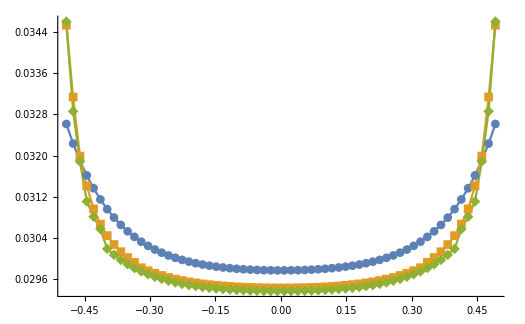

```mathematica
ListPlot[{residual0⟦All,{1,2}⟧,residual1⟦All,{1,2}⟧,residual2⟦All,{1,2}⟧},Joined->True,PlotMarkers->Automatic,PlotRange->Full]
```

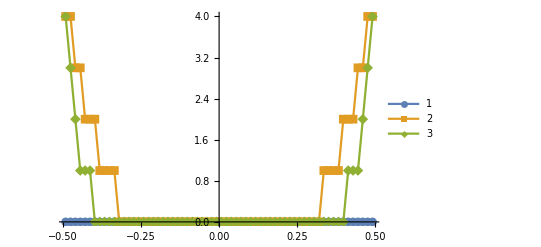

```mathematica
ListPlot[{residual0⟦All,{1,3}⟧,residual1⟦All,{1,3}⟧,residual2⟦All,{1,3}⟧},Joined->True,PlotMarkers->Automatic,PlotRange->Full,PlotLegends->Automatic]
```

```mathematica
ListPlot3D[{residual1⟦All,{1,2,3}⟧,residual0⟦All,{1,2,3}⟧},PlotRange->Full]
```

-Graphics3D-